# Solving TOV equations.

#### Constants

```mathematica
(* Universal constants*)
G = 6.6743 10^-8;
c = 2.99792458 10^10;

(* Astronomical parameters*)
Subscript[M, Earth]=5.9724*^27;
Subscript[R, Earth] = 6.371*^8;
Subscript[M, Jupiter]=1.8982*^30;
Subscript[R, Jupiter]=6.991*^9;
Subscript[M, sun]= 1.9885*^33;
Subscript[R, sun]=6.957*^10;

α=G Subscript[M, sun]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sun] c^2;

(* Nuclear parameters*)
mp=1.67262192369 10^-24;
mn=1.67492749804 10^-24;
me = 9.1093837015  10^-28;
λp=2.10308910336 10^-14;
λn =2.1001941552  10^-14;
λe = 3.8615926796  10^-11;

km = 10.0^5;
km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.860;
```

## 1 Equations of state:

## 1.1 Equation of state 1: Free gas of neutrons

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
kf[m_,l_]:=5((m c^2)/(15 π^2 l^3))^(0.4);
kn=kf[mn,λn];
kp=kf[mp,λp];
ke=kf[me,λe];

Density NR[p_]:=kn p^0.6
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
nfun[m_,l_]:= (m c^2)/(8 π^2 l^3)
epsilon i[z_,m_,l_]:= nfun[m,l]((2 z^3 + z )Sqrt[1 +z^2] - ArcSinh[z])
pressure i[z_,m_,l_]:=nfun[m,l]((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

```mathematica
ListEoS n={};
Do[ ListEoS n=Union[ListEoS n,Table[{pressure i[z,mn,λn],epsilon i[z,mn,λn]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-3,2}]
EoS n=Interpolation[ListEoS n,InterpolationOrder->1];
```

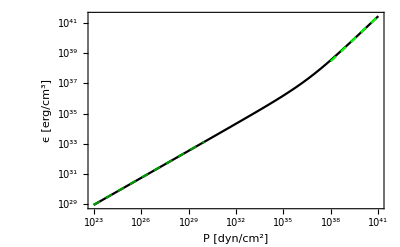

```mathematica
DNR=LogLogPlot[Density NR[x],{x,10^23, 10^30},
PlotStyle->{RGBColor[0.,0.6,0.],Dashed},
PlotLegends->Placed[{"Non Relativistic"},{Left,Top}]];
DR =LogLogPlot[Density R[x],{x,10^38, 10^41},
PlotStyle->{RGBColor[0.,1,0.], Dashed},
PlotLegends->Placed[{"Relativistic"},{Left,Top}]];
DNS=LogLogPlot[{EoS n[x]},{x,10^23,10^41},
PlotLegends->Placed[{"Whole range"},{Left,Top}],
PlotStyle->{ Black}];
EOSn =Show[{DNS,DNR, DR},
FrameLabel->{"P [dyn/cm^2]","ϵ [erg/cm^3]"},
Frame->True,
PlotTheme->"Scientific"]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/3-Neutron Stars Densities/Plots/equation_of_state_n_m.pdf", EOSn];
```

Now, let’s build the function for the whole range as a piecewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤  x<10^23}, {EoS n[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}}];
dener n[p_]:=pw/.x-> p
```

Now we can proceed to do the numerical integration

## 1.2 Equation of state 2: Free gas of npe

```mathematica
Zp[z_,mn_,mp_,me_]:=Sqrt[(mn^2 (1+z^2) - (me^2 + mp^2))^2-4 mp^2 me^2 ]/(2 mp mn Sqrt[1 + z^2])
Ze[z_,mn_,mp_,me_]:=mp/me Zp[z,mn,mp,me]

epsilon pe[z_]:=  epsilon i[z,mp,λp]+epsilon i[mp/me z, me, λe]
pressure pe[z_]:=pressure i[z,mp,λp]+pressure i[mp/me z ,me,λe]

epsilon npe[z_]:= epsilon i[z,mn,λn]+ epsilon i[Zp[z,mn,mp,me],mp,λp]+epsilon i[mp/me Zp[z,mn,mp,me],me,λe]
pressure npe[z_]:=pressure i[z,mn,λn]+pressure i[Zp[z,mn,mp,me],mp,λp]+pressure i[mp/me Zp[z,mn,mp,me],me,λe]
```

Non relativistic regime (before z_critical=Zc)

```mathematica
Zc=Zp[0,mn,mp,me]
{pressure pe[Zc],pressure npe[0]}
```

0.0012654

{3.03851×10^24,3.03851×10^24}

```mathematica
ListEoS npe=Table[{pressure pe[z],epsilon pe[z]},{z,0,Zc,10^-6}];
Do[ ListEoS npe=Union[ListEoS npe,Table[{pressure npe[z],epsilon npe[z]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-3,2}]
dener npe=Interpolation[ListEoS npe,InterpolationOrder->1];
```

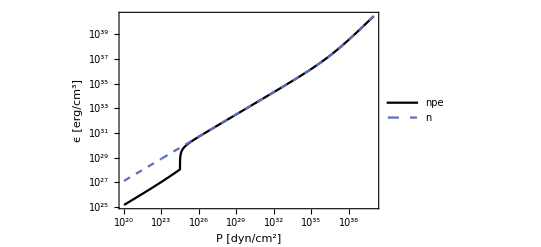

```mathematica
EOSnpe = LogLogPlot[{dener npe[x],dener n[x]},{x,10^20,10^40},
Frame->True,
FrameLabel->{"P [dyn/cm^2]","ϵ [erg/cm^3]"},
PlotStyle->{Black,Dashed},
PlotLegends->Placed[{"npe", "n"},{Left,Top}],
PlotTheme->"Scientific"]
```

```mathematica
Export["Plots/equation_of_state_npe_m.pdf",EOSnpe];
```

## 1.3 Equation of state 3: Interacting protons and neutrons

Auxiliary constants and functions

```mathematica
λN =2.1001941552  10^-1;  (*in fm*)
hbarc = 197.3269804 ;(*MeV fm*)

A := -46.65
B:=39.54
Bp:=0.3
σ := 1.663
C1:=-83.84
C2:=23.65
n0:=0.16
Subscript[pF, 0]:=263
mN :=939
EF:=3/5 Subscript[pF, 0]^2/(2 mN)
Λ1 :=1.5 Subscript[pF, 0]
Λ2 :=3 Subscript[pF, 0]
pF[n_]:= Subscript[pF, 0] (n/n0)^(1/3)
n[z_,l_]:= z^3/(3 π^2 l^3)
z[n_,l_]:= (3 π^2 l^3 n)^1/3
```

Energy density per baryon as function of baryon density:

```mathematica
EHalf[n_]:= mN+ EF (n/n0)^(2/3)+A/2 n/n0+ (B (n/n0)^σ)/(1 + Bp (n/n0)^(σ-1))+ 3 C1 (Λ1/Subscript[pF, 0])^3(pF[n]/Λ1-ArcTan[pF[n]/Λ1])+ 3 C2 (Λ2/Subscript[pF, 0])^3(pF[n]/Λ2-ArcTan[pF[n]/Λ2])
ESym[n_]:= 13 (n/n0)^(2/3)+ 17 n/n0
β[n_]:=(3 π^2 hbarc^3)/64 (13/n0^(2/3) n^(1/3) + 17/n0 n^(2/3))^-3
γ[n_]:=Sqrt[1+(2β[n])/27]
Yp[n_]:=1/2-1/4((4/27 β[n]^2/(γ[n]-1))^(1/3)-(2β[n](γ[n]-1))^(1/3))
ϵb[n_]:= n(EHalf[n]+(1-2Yp[n])^2 ESym[n] )
```

Pressure as function of baryon density, and in terms of energy density

```mathematica
Pb[n_]:= n((2EF)/3(n/n0)^(2/3)+A/2(n/n0)+ (σ B (n/n0)^σ)/(1 + Bp (n/n0)^(σ-1))-((σ-1) B Bp(n/n0)^(2σ-1))/((1 + Bp (n/n0)^(σ-1))^2)+  ( C1/(1 + (Subscript[pF, 0]/Λ1)^2(n/n0)^(2/3))+ C2/(1 + (Subscript[pF, 0]/Λ2)^2(n/n0)^(2/3)))(n/n0))+(1-2 Yp[n])^2 (26/3 n^(5/3)/n0^(2/3)+17 n^2/n0)
```

Conversion factors

```mathematica
MeVToErg:=1.6022 10^-6
fmTocm := 10^-13
MeVfmTocgs:= MeVToErg/fmTocm^3
```

Consistency test

```mathematica
{epsilon i[1,mn,λn], pressure i[1,mn,λn]}
```

{6.91787×10^36,8.43763×10^35}

```mathematica
{ϵb[n[1,λN]],Pb[n[1,λN]]}*MeVfmTocgs
```

{1.41986×10^37,1.18828×10^37}

Total energy density and pressure

```mathematica
ϵT[z_]:= ϵb[n[z,λN]]*MeVfmTocgs + epsilon i[mp/me Zp[z,mn,mp,me],me,λe]
PT[z_]:= Pb[n[z,λN]]*MeVfmTocgs+pressure i[mp/me Zp[z,mn,mp,me],me,λe]
```

List of z values and interpolation

```mathematica
0.1 n0
{ϵb[n0],Pb[n0]}*MeVfmTocgs
dener npe[5.78 10^33]
```

0.016

{2.43346×10^35,5.77616×10^33}

2.51342×10^35

```mathematica
ListEoS npe=Table[{pressure pe[z],epsilon pe[z]},{z,0,Zc,10^-6}];
ListEoS int={};
Do[ ListEoS int=Union[ListEoS int,Table[{PT[z],ϵT[z]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-4,0}]
dener int=Interpolation[ListEoS int,InterpolationOrder->1];
```

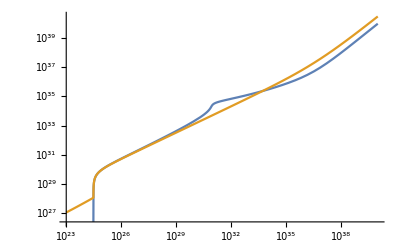

```mathematica
LogLogPlot[{dener int[x],dener npe[x]},{x,10^23,10^40}]
```

## 2. Hydrostatic Equilibrium equation

## 2.1 Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
ListRG={};
Do[
Do[{
solutionN = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solutionN[[1]];
pressure ad[x_]:=p[x]/.solutionN[[1]];
If[pressure ad[rad]==0,
Print["Central Pressure = ", Pc, "\n",
	"Radius in km = ", rad, "\n",
	"Mass in M_s = ", mass ad[rad]];
Break[],
ListRG=Append[ListRG,{rad,dener[Pc*pressure ad[rad]]}]
];
},
{rad,1,25,.1}],{dener,{dener n,dener npe}}]
```

Central Pressure = 3.3×10^34
Radius in km = 14.8
Mass in M_s = 0.804716

$Aborted

## 2.2 TOV equations and density

### 2.2.1 Equation of state with only neutrons

Computation with precision of masses and radii

```mathematica
ListPc ={ 10.^35,10.^36, 10.^38, 10.^40};
Do[{
Do[{
Do[{
Pc = ListPc[[ñ]];
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[TOVpressure[rad]==0,
Break[],
R = rad;
MT = mass[rad]
];
},{rad,rmin+.001,30,.001}];
Print[Pc, "\t",R, "\t",MT]
},{dener,{dener n,dener npe}}]}
,{ñ,1,Length[ListPc]}]
```

1.×10^35	11.339	0.674623

1.×10^35	11.323	0.66734

1.×10^36	7.68	0.688051

1.×10^36	7.666	0.674761

1.×10^38	5.147	0.378706

1.×10^38	5.143	0.368554

1.×10^40	6.27	0.44043

1.×10^40	6.322	0.430662

Computation of density and mass distribution for different Pc, gives the same for both EOS

```mathematica
ListPc ={ 10.^35,10.^36, 10.^38, 10.^40};
Listϵ=Table[0,{n,Length[ListPc]}];
Listm=Table[0,{n,Length[ListPc]}];

Do[{
Localϵ={};
Localm={};
Do[{
Pc = ListPc[[ñ]];
dener=dener n;
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[TOVpressure[rad]==0,
Break[],
Localϵ=Append[Localϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
Localm=Append[Localm,{rad,mass[rad]}];
];
},{rad,rmin+.01,30,.1}],
Listϵ[[ñ]]=Localϵ;
Listm[[ñ]]=Localm
},{ñ,1,Length[ListPc]}]
```

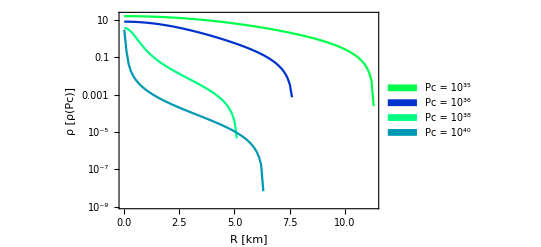

```mathematica
DensityNS =ListLogPlot[{ Listϵ[[1]],Listϵ[[2]],Listϵ[[3]],Listϵ[[4]]},
PlotStyle->{RGBColor[0,1,0.3],RGBColor[0,0.2,0.8],RGBColor[0,1,0.5],RGBColor[0,0.6,0.7]},
Joined->True,
Frame->True,
FrameLabel->{"R [km]", "ρ [ρ(Pc)]"},
PlotLegends->Placed[SwatchLegend[{RGBColor[0,1,0.3],RGBColor[0,0.2,0.8],RGBColor[0,1,0.5],RGBColor[0,0.6,0.7]},
{"Pc = 10^35 ","Pc = 10^36 ","Pc = 10^38", "Pc = 10^40"},
LegendMarkers->"Bubble",
LegendMarkerSize->10,
LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],
{Right, Bottom}]]
```

```mathematica
Export["Plots/densityNS_n.pdf",DensityNS]
```

Plots/densityNS_n.pdf

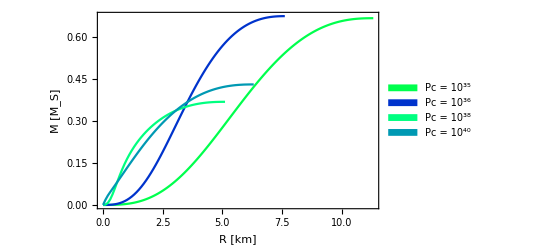

```mathematica
MassNS=ListPlot[{Listm[[1]],Listm[[2]], Listm[[3]],Listm[[4]]},PlotStyle->{RGBColor[0,1,0.3],RGBColor[0,0.2,0.8],RGBColor[0,1,0.5],RGBColor[0,0.6,0.7]},
Joined->True,
Frame->True,
FrameLabel->{"R [km]", "M [M_S]"},
PlotLegends->Placed[SwatchLegend[{RGBColor[0,1,0.3],RGBColor[0,0.2,0.8],RGBColor[0,1,0.5],RGBColor[0,0.6,0.7]},
{"Pc = 10^35 ","Pc = 10^36 ","Pc = 10^38", "Pc = 10^40"},
LegendMarkers->"Bubble",
LegendMarkerSize->10,
LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],
{Right, Bottom}]]
```

```mathematica
Export["Plots/MassNS_n.pdf",MassNS];
```

## 2.3 Traversal Times

### 2.3.1 Theory

The equations to solve are, in non dimensional form

```mathematica
(d p)/(d r)= -(α [M(r) + β(Pc) r^3 p(r)][ϵ(p(r)) + p(r)][r^2 - 2 α r M(r)])^-1
```

This gives us non dimensional pressure and energy density. Along with the non-dimensional mass, this will be useful to define the metric tensor component functions:

```mathematica
Subscript[g, rr](r)=A(r) = (1 - (2 G M(r))/r)^-1 = (1 - 2α (M̄)/r)^-1
```

with M̄ in units of solar masses and r in km. And the other function comes from the diff. eq.

```mathematica
(B'(r))/(B(r))= - (2 P'(r))/(P(r)+ϵ(r))
```

with boundary conditions in the surface equal to the Schwarzschild solution for the exterior metric.
Given  A=g_rr and B=g_tt, we already have all the components of the metric. The general energy diff. eq. is

```mathematica
1/2(dr/dτ)^2+1/2 g^rr(r)(1 - g^tt(r) E^2)c^2=0
```

from this energy-like equation, consider the potential part, at the turning points (r=R),

```mathematica
V(R) = 1/2 g^rr(R)(1 - g^tt(R) E^2)c^2=0
E^2= 1/(g^tt(R))= Subscript[g, tt](R) 
-> E^2 = B(R)
```

we have therefore the following integral:

```mathematica
Δτ = 2/c∫(√(-Subscript[g, tt](r)))/(√(1 - E^2/Subscript[g, rr](r)))ⅆr
Δτ = 2/c(∫_0)^R(√(A(r)B(r)))/(√(B(R)- B(r)))ⅆr
```

that gives us proper times in seconds.

### 2.2.2 Numerical Computation

Schwarzschild times

```mathematica
Rhat[R_, M_]:= Sqrt[(G M)/(c^2 R)]
Em[R_]:=√(1-2 R^2)
x[r_,R_]:= Sqrt[1-2r^2]/Sqrt[1-2 R^2]
ω [R_,M_] :=Sqrt[ (G M)/R^3]
τ[R_]:=2 Re[NIntegrate[1/(x[r,R] Em[R])(3-x[r,R])/Sqrt[(5-x[r,R])(x[r,R]-1)],{r,0,R},WorkingPrecision->10, AccuracyGoal->20]]

t[R_]:= 2 NIntegrate[Re[4/(Em[R]^2x[r,R](3-x[r,R])Sqrt[(5 - x[r,R])(x[r,R]-1)] )],{r,0,R},WorkingPrecision->10, AccuracyGoal->20]
```

The following is the code that returns proper times for some NS’s with different central pressures:

```mathematica
ListPc ={ 10.^35, 10.^36, 10.^38, 10.^40};
Do[{
Pc = ListPc[[ñ]];

Print["NS ", ñ, " - Central Pressure: ", ScientificForm[Pc]]; 

Do[{
Listϵ={};
Listp={};

Do[{

(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[TOVpressure[rad]==0,
Break[],
Listϵ=Append[Listϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
Listp=Append[Listp,{rad,TOVpressure[rad]}];
R=rad;
MStar=mass[rad];
];
},{rad,rmin+0.001,14,.001}];

Print["R (km) = ", R, "\n",
	"M  (M_s)  ", MStar, "\n",
	"R̂     =  ", Rhat[R km, MStar*Subscript[M, sun]]],


ϵ n= Interpolation[Listϵ,InterpolationOrder->10];
p n =Interpolation[Listp,InterpolationOrder->10];

(**** Metric coefficients ****)

A[r_]:= (1 - 2 α mass[r]/r)^-1;

Bmax =1- (2 α)/R;
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] p n'[r]/(p n[r]+ϵ n[r]),Bb[R]== Bmax},Bb[r],{r,rmin+0.1,R}];
B[r_]=Bb[r]/.BFunction[[1]];

(****Computing times ****)

τsNS =2 NIntegrate[Sqrt[A[r] B[r]/(B[R]-B[r])],{r,rmin,R}]/(10^(-5) c);
tsNS =2 NIntegrate[Sqrt[A[r] B[R]/(B[r](B[R]-B[r]))],{r,rmin,R}]/(10^(-5) c);

Print["τ (ms): ", τsNS 10^3,"\n",
	"t  (ms): ", tsNS 10^3, "\n",
	"τs (ms): ", τ[Rhat[R km, MStar*Subscript[M, sun]]] 10^3/ω[R km, MStar*Subscript[M, sun]],"\n",
	"ts (ms): ", t[Rhat[R km, MStar*Subscript[M, sun]]]10^3/ω[R km, MStar*Subscript[M, sun]],"\n",
"----------------------------------------"]},{dener,{dener npe}}]
},{ñ,1,Length[ListPc]}]
```

NS 1 - Central Pressure: 1.×10^35

R (km) = 11.323
M  (M_s)  0.66734
R̂     =  0.295011

NDSolve::ndsz: At r == 11.323, step size is effectively zero; singularity or stiff system suspected.

NIntegrate::zeroregion: Integration region {{11.323,11.323000000000000042709983600374930209438168961558099117332938178}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

τ (ms): 0.+0.0816677 ⅈ
t  (ms): 0.+0.0000453323 ⅈ
τs (ms): 0.380606
ts (ms): 0.44071
----------------------------------------

NS 2 - Central Pressure: 1.×10^36

Computation of times vs central pressure and radius vs central pressure

```mathematica
ListPc ={ 10.^33,5 10.^33,10.^34,5 10.^34,10.^35,5 10.^35, 10.^36,5 10.^36,10.^37,5 10.^37, 10.^38,5 10.^38,10.^39,5 10.^39, 10.^40,5 10.^40};
AnalysRhat={};
Analysτ = {};
Analyst = {};
Do[{
Pc = ListPc[[ñ]];
Listϵ={};
Listp={};

Do[{

(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[TOVpressure[rad]==0,
Break[],
Listϵ=Append[Listϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
Listp=Append[Listp,{rad,TOVpressure[rad]}];
R=rad;
MStar=mass[rad];
];
},{rad,rmin+0.1,30,.1}];

ϵ n= Interpolation[Listϵ,InterpolationOrder->10];
p n =Interpolation[Listp,InterpolationOrder->10];

(**** Metric coefficients ****)

A[r_]:= (1 - 2 α mass[r]/r)^-1;

Bmax =1- (2 α)/R;
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] p n'[r]/(p n[r]+ϵ n[r]),Bb[R]== Bmax},Bb[r],{r,rmin+0.1,R}];
B[r_]=Bb[r]/.BFunction[[1]];

(****Computing times ****)

τsNS =2 NIntegrate[Sqrt[A[r] B[r]/(B[R]-B[r])],{r,rmin,R}]/(10^(-5) c);
tsNS =2 NIntegrate[Sqrt[A[r] B[R]/(B[r](B[R]-B[r]))],{r,rmin,R}]/(10^(-5) c);
Print[Pc,"\t", Rhat[R km, MStar*Subscript[M, sun]],"\t",τsNS, "\t", tsNS],
AnalysRhat = Append[AnalysRhat,{Pc, Rhat[R km, MStar*Subscript[M, sun]]}],
Analysτ = Append[Analysτ,{Rhat[R km, MStar*Subscript[M, sun]],τsNS }],
Analyst = Append[Analyst,{Rhat[R km, MStar*Subscript[M, sun]],tsNS }]
},{ñ,1,Length[ListPc]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {20.9735}. NIntegrate obtained 185.71+19.0265 ⅈ and 0.0709285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {20.9735}. NIntegrate obtained 204.208+20.5243 ⅈ and 0.0765123 for the integral and error estimates.

1.×10^33	0.143627	0.00123892+0.000126931 ⅈ	0.00136233+0.000136923 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {17.299}. NIntegrate obtained 115.55+5.20793 ⅈ and 0.0531895 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

5.×10^33	0.190921	0.000770869+0.0000347436 ⅈ	0.000876676+0.0000381522 ⅈ

1.×10^34	0.214202	0.000604563+0.0000387321 ⅈ	0.000702532+0.0000429532 ⅈ

5.×10^34	0.27177	0.000378057	0.000468849

1.×10^35	0.296904	0.000301926	0.000390059

5.×10^35	0.348619	0.000190812	0.000278805

1.×10^36	0.365607	0.000158431	0.000247956

5.×10^36	0.384997	0.000111853	0.000210396

1.×10^37	0.382405	0.000102978	0.000208162

5.×10^37	0.350923	0.0000982263+0.0000131144 ⅈ	0.000213065+0.0000207888 ⅈ

1.×10^38	0.331105	0.000108142+0.0000141394 ⅈ	0.000223634+0.0000217737 ⅈ

5.×10^38	0.302036	0.000145777+0.0000178234 ⅈ	0.000257839+0.0000245787 ⅈ

1.×10^39	0.303965	0.000131839	0.00023745

5.×10^39	0.318745	0.000117808	0.000223135

1.×10^40	0.323853	0.000142282+0.0000167344 ⅈ	0.000257976+0.0000231223 ⅈ

5.×10^40	0.324506	0.000122334	0.000233001

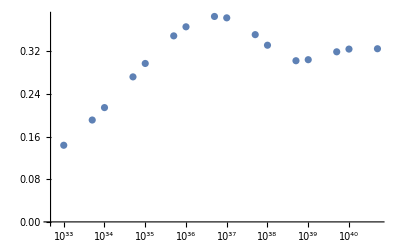

```mathematica
ListLogLinearPlot[AnalysRhat]
```

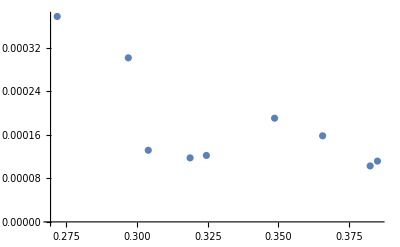

```mathematica
ListPlot[Analysτ]
```

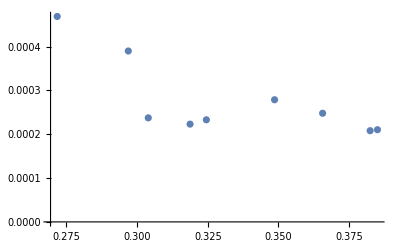

```mathematica
ListPlot[Analyst]
```